## This file used to be BC_FirstTryTOSS

```mathematica
WantDetails="NoWantDetails";
```

#### Choose Tmat, then check

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrownTypo;
```

```mathematica
Tmat=TmatBrownNew;
```

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatDefeat;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

Tmat is TmatSSA2023

The [T]_𝔹𝔹 matrix is (0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901)

The eigenvalues are: {0.965054,0.701544,0.060227,0.0422136,0.0158499,0.0123903}

The Voigt matrix is (0.357328 | 0.0423998 | 0.344492 | -0.176408 | -0.0397992 | -0.0419674
0.0423998 | 0.209533 | 0.0934665 | 0.0427684 | -0.0605007 | 0.170826
0.344492 | 0.0934665 | 0.419451 | -0.166206 | -0.0740327 | 0.0186476
-0.176408 | 0.0427684 | -0.166206 | 0.158541 | -0.00329258 | 0.113931
-0.0397992 | -0.0605007 | -0.0740327 | -0.00329258 | 0.03673 | -0.057429
-0.0419674 | 0.170826 | 0.0186476 | 0.113931 | -0.057429 | 0.210212)

10-7-2023 8:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 0.86278   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.806 = 46.19^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (0.229654 | 0. | 0. | 0. | 0. | 0.
0. | 0.229654 | 0. | 0. | 0. | 0.
0. | 0. | 0.229654 | 0. | 0. | 0.
0. | 0. | 0. | 0.229654 | 0. | 0.
0. | 0. | 0. | 0. | 0.229654 | 0.
0. | 0. | 0. | 0. | 0. | 0.64901)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.139785 and μ = 0.114827, Poisson is 0.274506

#### Choose TRIG-CUBE path

```mathematica
Σn[0]=TRIV;
Σn[1]=MONO;
Σn[2]=TRIG;
Σn[3]=CUBE;
Σn[4]=ISO;
nMax=4;
Σn/@Range[0,nMax]
```

{TRIV,MONO,TRIG,CUBE,ISO}

#### Or choose TET-XISO path

```mathematica
Σn[0]=TRIV;
Σn[1]=MONO;
Σn[2]=ORTH;
Σn[3]=TET;
Σn[4]=XISO;
Σn[5]=ISO;
nMax=5;
Σn/@Range[0,nMax]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

```mathematica
ListΣ=Σn/@Range[0,nMax]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

#### OutputFor (Pathway 2)

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
OutputFor[Tmat,Σn[#]]&/@Range[0,nMax]
```

Tmat is TmatSSA2023

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

10-7-2023 8:23

𝒯_TRIV = 𝒯

d(T, 𝒯_TRIV) = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯_TRIV) = 0           ''

10-7-2023 8:23

NMinimize = {0.221763,{θ→0.308498,σ→0.601871,ϕ→0.955228}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {17.7,0.,54.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.550163 | -0.303627 | 0.777902
0.175321 | 0.952791 | 0.247895
-0.816445 | 0 | 0.577423)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-7-2023 8:23

NMinimize = {0.333256,{θ→1.25013,σ→-2.05905,ϕ→1.13962}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {71.6,-118.,65.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.776336 | 0.561519 | 0.286354
-0.46443 | 0.202432 | 0.862164
0.426154 | -0.80232 | 0.417941)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

10-7-2023 8:23

NMinimize = {0.398609,{θ→3.49223,σ→2.34379,ϕ→0.632284}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {200.1,134.3,36.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.774898 | 0.302447 | -0.55503
-0.478779 | 0.854144 | -0.203001
0.412678 | 0.423042 | 0.80668)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

10-7-2023 8:23

NMinimize = {0.548649,{θ→1.27187,σ→1.41779,ϕ→1.16293}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {72.9,0.,66.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.116812 | -0.955654 | 0.270334
0.379065 | 0.294492 | 0.87726
-0.917968 | 0 | 0.396655)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

10-7-2023 8:23

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 0.86278   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.806 = 46.19^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (0.229654 | 0. | 0. | 0. | 0. | 0.
0. | 0.229654 | 0. | 0. | 0. | 0.
0. | 0. | 0.229654 | 0. | 0. | 0.
0. | 0. | 0. | 0.229654 | 0. | 0.
0. | 0. | 0. | 0. | 0.229654 | 0.
0. | 0. | 0. | 0. | 0. | 0.64901)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.139785 and μ = 0.114827, Poisson is 0.274506

{Null,Null,Null,Null,Null,Null}

#### OutputFor (Pathway 3) ClosestToPrevious[n, Tmat] has symmetry Σn[n].

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
OutputFor[ClosestToPrevious[#,Tmat],Σn[#+1]]&/@Range[0,nMax-1]
```

Tmat is TmatSSA2023

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

10-7-2023 8:23

NMinimize = {0.221763,{θ→0.308498,σ→0.601871,ϕ→0.955228}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {17.7,0.,54.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.550163 | -0.303627 | 0.777902
0.175321 | 0.952791 | 0.247895
-0.816445 | 0 | 0.577423)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-7-2023 8:24

NMinimize = {0.274585,{θ→1.9079,σ→-2.18694,ϕ→1.53038}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {109.3,-125.3,87.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.777902 | 0.534462 | -0.330484
0.247895 | 0.222261 | 0.942946
0.577423 | -0.815445 | 0.0404068)  (A ORTH-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

10-7-2023 8:24

NMinimize = {0.212907,{θ→0.6137,σ→-1.06883,ϕ→2.50355}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {35.2,-61.2,143.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.188888 | -0.852768 | 0.486937
-0.93925 | -0.0121775 | 0.343018
-0.286585 | -0.522148 | -0.803262)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

10-7-2023 8:24

NMinimize = {0.175202,{θ→1.27239,σ→-2.36917,ϕ→0.37168}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {72.9,0.,21.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.27392 | -0.955807 | 0.106773
0.890543 | 0.293995 | 0.347131
-0.363181 | 0 | 0.931719)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

10-7-2023 8:24

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 1.24127×10^-16   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0 (Angle betweem T and 𝒯_ISO. The initial β_ISO^T = 1.5×10^-16 is here chopped to zero, since the chop threshold is set at 0.01^o)

Since β_ISO^(□  T) = 0, then T is assigned symmetry ISO.

Lamé parameters for T are λ = 0.139785 and μ = 0.114827, Poisson is 0.274506

{Null,Null,Null,Null,Null}

#### Elastic maps at the nodes on Pathway 2

```mathematica
SmatOfN[n_,pw2]:=Closest[Tmat,Σn[n]];
```

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Chop[MatrixForm[SmatOfN[#,pw2]],0.0001]&/@Range[0,nMax]
```

Tmat is TmatSSA2023

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

{(0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901),(0.304531 | -0.0444525 | 0.238839 | 0.184171 | 0.0910856 | -0.181699
-0.0444525 | 0.101994 | -0.162948 | -0.0406421 | 0.0311181 | -0.146695
0.238839 | -0.162948 | 0.447641 | 0.195593 | 0.00627892 | 0.179027
0.184171 | -0.0406421 | 0.195593 | 0.19617 | 0.0734069 | -0.0951994
0.0910856 | 0.0311181 | 0.00627892 | 0.0734069 | 0.0979336 | -0.184171
-0.181699 | -0.146695 | 0.179027 | -0.0951994 | -0.184171 | 0.64901),(0.328191 | -0.0151825 | 0.237975 | 0.251598 | 0.0356475 | -0.154287
-0.0151825 | 0.136827 | -0.0621318 | -0.022131 | 0.0421271 | -0.217364
0.237975 | -0.0621318 | 0.310507 | 0.226683 | 0.0250874 | -0.0114825
0.251598 | -0.022131 | 0.226683 | 0.28432 | 0.0466913 | -0.136607
0.0356475 | 0.0421271 | 0.0250874 | 0.0466913 | 0.0884237 | -0.145487
-0.154287 | -0.217364 | -0.0114825 | -0.136607 | -0.145487 | 0.64901),(0.294916 | -0.0478776 | 0.245978 | 0.212267 | 0.0151767 | -0.0882431
-0.0478776 | 0.165882 | -0.107722 | -0.0452436 | 0.0508153 | -0.241268
0.245978 | -0.107722 | 0.349134 | 0.223427 | -0.0156105 | 0.060715
0.212267 | -0.0452436 | 0.223427 | 0.249039 | 0.0117127 | -0.071898
0.0151767 | 0.0508153 | -0.0156105 | 0.0117127 | 0.0892975 | -0.148121
-0.0882431 | -0.241268 | 0.060715 | -0.071898 | -0.148121 | 0.64901),(0.320525 | 0.057938 | 0.159214 | 0.219613 | 0.122422 | -0.157686
0.057938 | 0.150365 | 0.0256093 | 0.0836471 | 0.0377252 | -0.0485923
0.159214 | 0.0256093 | 0.195424 | 0.167336 | 0.0528437 | -0.107469
0.219613 | 0.0836471 | 0.167336 | 0.327199 | 0.0775993 | -0.157815
0.122422 | 0.0377252 | 0.0528437 | 0.0775993 | 0.154756 | -0.0690706
-0.157686 | -0.0485923 | -0.107469 | -0.157815 | -0.0690706 | 0.64901),(0.229654 | 0 | 0 | 0 | 0 | 0
0 | 0.229654 | 0 | 0 | 0 | 0
0 | 0 | 0.229654 | 0 | 0 | 0
0 | 0 | 0 | 0.229654 | 0 | 0
0 | 0 | 0 | 0 | 0.229654 | 0
0 | 0 | 0 | 0 | 0 | 0.64901)}

#### Elastic maps for the nodes on Pathway 3

```mathematica
SmatOfN[n_,pw3]:=ClosestToPrevious[n,Tmat];
```

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Chop[MatrixForm[SmatOfN[#,pw3]],0.0001]&/@Range[0,nMax]
```

{(0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901),(0.304531 | -0.0444525 | 0.238839 | 0.184171 | 0.0910856 | -0.181699
-0.0444525 | 0.101994 | -0.162948 | -0.0406421 | 0.0311181 | -0.146695
0.238839 | -0.162948 | 0.447641 | 0.195593 | 0.00627892 | 0.179027
0.184171 | -0.0406421 | 0.195593 | 0.19617 | 0.0734069 | -0.0951994
0.0910856 | 0.0311181 | 0.00627892 | 0.0734069 | 0.0979336 | -0.184171
-0.181699 | -0.146695 | 0.179027 | -0.0951994 | -0.184171 | 0.64901),(0.204382 | -0.0311103 | 0.0733024 | 0.125232 | 0.0714138 | -0.15935
-0.0311103 | 0.274887 | 0.051893 | -0.119979 | 0.000642399 | -0.226207
0.0733024 | 0.051893 | 0.385686 | 0.00590279 | -0.0443999 | 0.0965977
0.125232 | -0.119979 | 0.00590279 | 0.184002 | 0.0560389 | -0.0345397
0.0714138 | 0.000642399 | -0.0443999 | 0.0560389 | 0.0993116 | -0.156213
-0.15935 | -0.226207 | 0.0965977 | -0.0345397 | -0.156213 | 0.64901),(0.225216 | -0.0135865 | -0.0124208 | 0.0614039 | 0.104043 | 0
-0.0135865 | 0.317269 | -0.00133488 | -0.0338804 | 0.0371691 | 0
-0.0124208 | -0.00133488 | 0.327264 | 0.00863897 | 0.0117662 | 0
0.0614039 | -0.0338804 | 0.00863897 | 0.111249 | 0.0398601 | 0
0.104043 | 0.0371691 | 0.0117662 | 0.0398601 | 0.167271 | 0
0 | 0 | 0 | 0 | 0 | 0.64901),(0.229654 | 0 | 0 | 0 | 0 | 0
0 | 0.229654 | 0 | 0 | 0 | 0
0 | 0 | 0.229654 | 0 | 0 | 0
0 | 0 | 0 | 0.229654 | 0 | 0
0 | 0 | 0 | 0 | 0.229654 | 0
0 | 0 | 0 | 0 | 0 | 0.64901),(0.229654 | 0 | 0 | 0 | 0 | 0
0 | 0.229654 | 0 | 0 | 0 | 0
0 | 0 | 0.229654 | 0 | 0 | 0
0 | 0 | 0 | 0.229654 | 0 | 0
0 | 0 | 0 | 0 | 0.229654 | 0
0 | 0 | 0 | 0 | 0 | 0.64901)}

#### Angle between the elastic maps at adjacent nodes.

```mathematica
AngleToNextFrom[n_,Tmat_,pw_]:=AngleMatrix[SmatOfN[n+1,pw],SmatOfN[n,pw]]
```

#### Examples.

```mathematica
AngleToNextFrom[#,Tmat,pw2]/Degree&/@Range[0,nMax-2]
```

{10.6898,19.8642,11.3122,31.4819}

```mathematica
AngleToNextFrom[#,Tmat,pw3]/Degree&/@Range[0,nMax-1]
```

{10.6898,29.1479,31.9098,18.1576,1.20742×10^-6}

```mathematica
yy[0,Tmat_,pw_]:=0;
yy[n_,Tmat_,pw_]:=yy[n-1,Tmat,pw]+AngleToNextFrom[n-1,Tmat,pw];
```

```mathematica
ydiff[n_,Tmat_]:=yy[n,Tmat,pw2]-yy[n,Tmat,pw3]
dymax=Max[ydiff[#,Tmat]&/@Range[0,nMax]]
```

0.38855

#### Examples.

```mathematica
yy[#,Tmat,pw2]/Degree&/@Range[0,nMax]
```

{0,10.6898,30.554,41.8662,73.3482,112.167}

```mathematica
yy[#,Tmat,pw3]/Degree&/@Range[0,nMax]
```

{0,10.6898,39.8377,71.7475,89.9051,89.9051}

```mathematica
ydiff[#,Tmat]/Degree&/@Range[0,nMax]
```

{0,0.,-9.2837,-29.8812,-16.5569,22.2623}

```mathematica
WantPW3="WantPW3"
```

WantPW3

```mathematica
(* WantPW3="NoWantPW3" *)
```

#### The Pathway 1 “curves” are just colored line segments (hues are set in chooseTmat.nb):

```mathematica
BetaSeg[i_]:={hue[ListΣ[[i+1]] ],Line[{{0,0},{i,AngleMatrix[Tmat,Closest[Tmat,ListΣ[[i+1]] ]]/Degree}}],Point[{i,AngleMatrix[Tmat,Closest[Tmat,ListΣ[[i+1]]  ]]/Degree}]}
```

#### Main plot

Tmat is TmatSSA2023

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

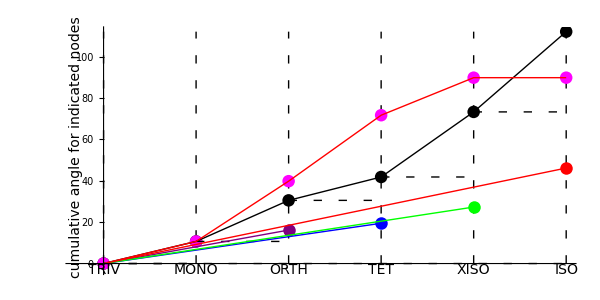

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],Line[{{0,0},{nMax,0}}],
Table[Line[{{n,0},{n,yy[nMax,Tmat,pw2]/Degree}}],{n,0,nMax}]},     (* vertical dashed lines *)
Point[{#,yy[#,Tmat,pw2]/Degree}]&/@Range[0,nMax],   (* pw2 *)
If[WantPW3=="WantPW3",
{Magenta,PointSize[.015],Point[{#,yy[#,Tmat,pw3]/Degree}]&/@Range[0,nMax]}], (* pw3 *)
{Dashing[{.01,.02}],         (* horizontal dashed steps, pw2 only*)
Line[{{#,      yy[#,Tmat,pw2]/Degree},
   {#+1,yy[#,Tmat,pw2]/Degree}}]&/@Range[0,nMax-1]},
 Line[{#,yy[#,Tmat,pw2]/Degree}&/@Range[0,nMax]],      (* the main polygonal line, pw2 *)
If[WantPW3=="WantPW3",
{Red,Line[{#,yy[#,Tmat,pw3]/Degree}&/@Range[0,nMax]]}],  (* the main polygonal line, pw3 *)
BetaSeg[#]&/@Range[2,nMax],
Text[Style[Σn[#],14],{#,-3}]&/@Range[0,nMax],
Text[Style["cumulative angle for indicated nodes",14],{-.3,.5yy[nMax,Tmat,pw2]/Degree},{0,0},{0,1}]},AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},AxesOrigin->{0,0}]
```

#### Difference between Pathway 2 and 3

Tmat is TmatSSA2023

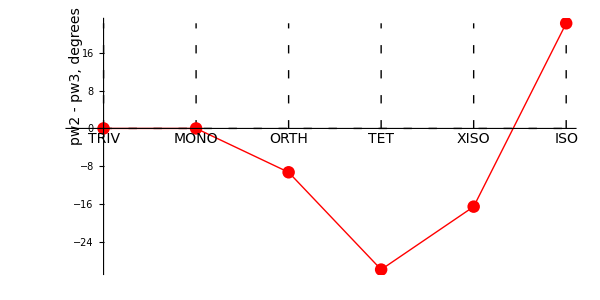

```mathematica
MatrixNote[Tmat]
Graphics[{
{Dashing[{.01,.02}],Line[{{0,0},{5,0}}],Table[Line[{{n,0},{n,dymax/Degree}}],{n,0,5}]},
{Red,PointSize[.015],Point[{#,ydiff[#,Tmat]/Degree}]&/@Range[0,5]}, (* points *)
{Red,Line[{#,ydiff[#,Tmat]/Degree}&/@Range[0,5]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax/Degree}]&/@Range[0,5],
Text[Style["pw2 - pw3, degrees",14],{-.3,.5dymax/Degree},{0,0},{0,1}]},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> False,AxesOrigin->{0,0}]
```

## BrownTypo

Tmat is TmatBrownTypo

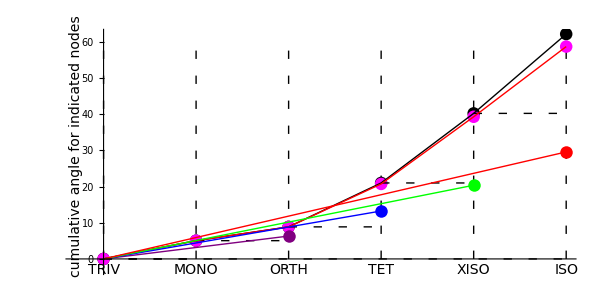

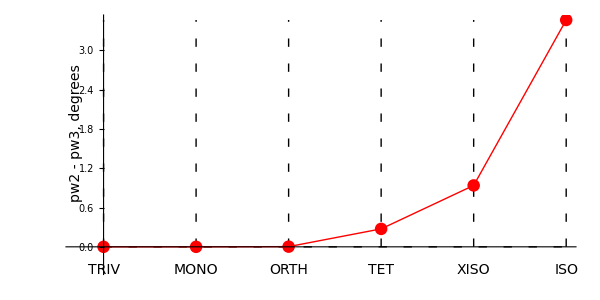

## BrownNew

Tmat is TmatBrownNew

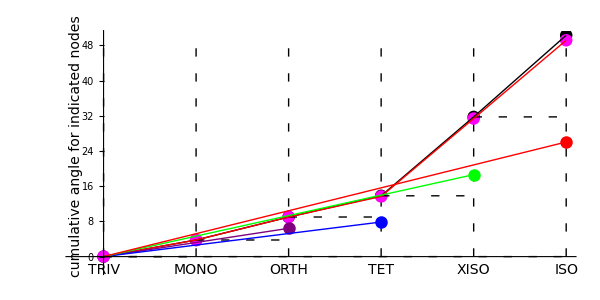

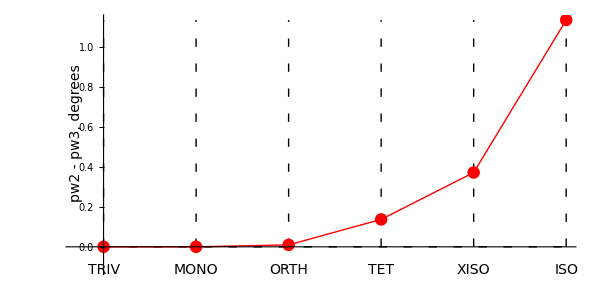

## SSA2023 -- unexpected results

Tmat is TmatSSA2023

-Graphics-

-Graphics-

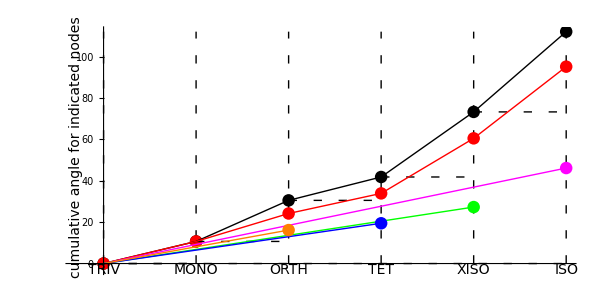

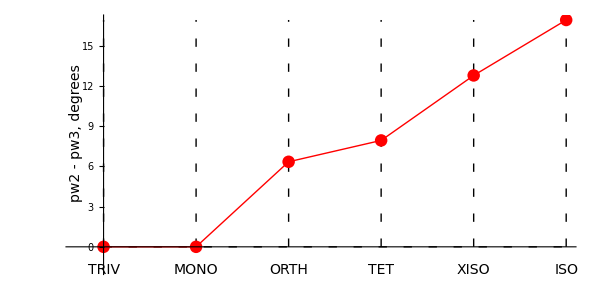

## Defeat

Tmat is TmatDefeat

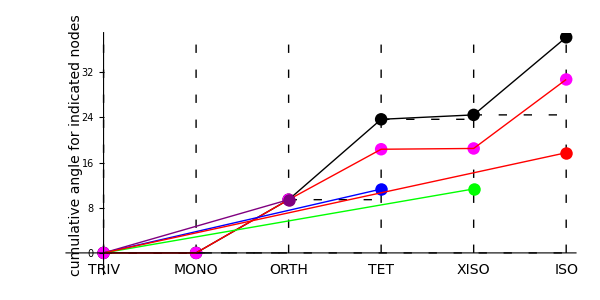

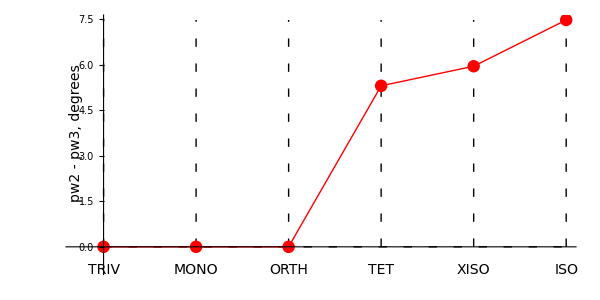

## Mar17

Tmat is TmatMar17

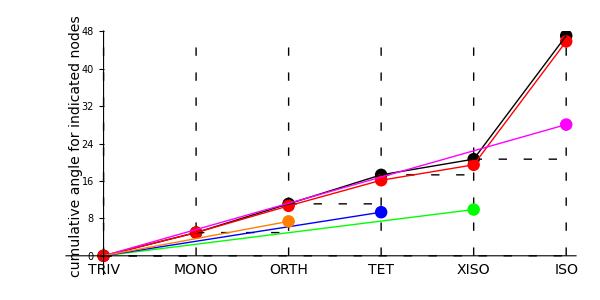

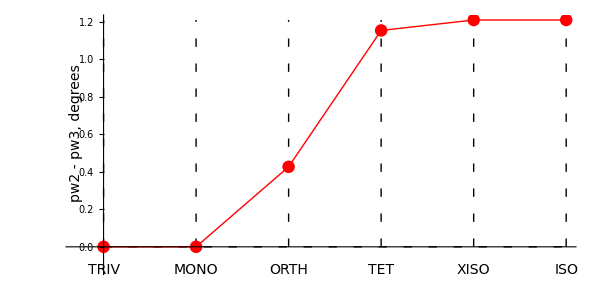

## Igel